```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
Consts=KerrGeoConstantsOfMotion[.998,10,0,Cos[π/4]]
```

<|ℰ→0.952846,ℒ→2.4798,𝒬→6.19527|>

```mathematica
Freqs=KerrGeoFrequencies[.998,10,0,Cos[π/4]]
```

<|Ω_r→0.0233628,Ω_θ→0.0296339,Ω_ϕ→0.0312778|>

```mathematica
orbit = KerrGeoOrbit[.998,10,0,Cos[π/4]];
{tt,rt,θt,ϕt}=orbit["Trajectory"];
```

OptionValue::nodef: Unknown option Time for KerrGeoOrbit.

```mathematica
Δ[r_]:=r^2-2M r+a^2
```

```mathematica
M=1;
a=.998;
r0=10;
γ = Consts[[1]](((r0^2+a^2)^2)/Δ[r0]-a^2)+a Consts[[2]](1-(r0^2+a^2)/Δ[r0]);
δ=a Consts[[1]]((r0^2+a^2)/Δ[r0]-1)-(a^2 Consts[[2]])/Δ[r0];
β = a^2(1-Consts[[1]]^2);
l=1;
m=1;
k=1;

zm[M_,a_,En_,L_,Q_]:=1/(2 (a^2-a^2 En^2))(a^2-a^2 En^2+L^2+Q-√((-a^2+a^2 En^2-L^2-Q)^2-4 (a^2-a^2 En^2) Q))
zp[M_,a_,En_,L_,Q_]:=1/(2 (a^2-a^2 En^2))(a^2-a^2 En^2+L^2+Q+√((-a^2+a^2 En^2-L^2-Q)^2-4 (a^2-a^2 En^2) Q))
```

```mathematica
Zm=zm[M,a,Consts[[1]],Consts[[2]],Consts[[3]]]
Zp=zp[M,a,Consts[[1]],Consts[[2]],Consts[[3]]]
```

0.5

135.096

```mathematica
dt[χ_]:=(γ+a^2 Consts[[1]]Zm Cos[χ]^2)/(√(β(Zp-Zm Cos[χ]^2)))
```

```mathematica
tp[χ0_]:=NIntegrate[dt[χ],{χ,0,χ0}]
ϕp[χ0_]:=NIntegrate[1/(√(β(Zp-Zm Cos[χ]^2)))(Consts[[2]]/(1-Zm Cos[χ]^2)+δ),{χ,0,χ0}]
dθ[χ0_]:=Piecewise[{{√((Zm(1-Cos[χ0]^2))/(1-Zm Cos[χ0]^2)),0<Mod[χ0,2π]≤π},{-√((Zm(1-Cos[χ0]^2))/(1-Zm Cos[χ0]^2)),0<Mod[χ0,2π]<2π}}];
Θ=θ/.NDSolve[{θ'[χ0]==dθ[χ0],θ[0]==ArcCos[√Zm]},θ,{χ0,0,2π}][[1]];
```

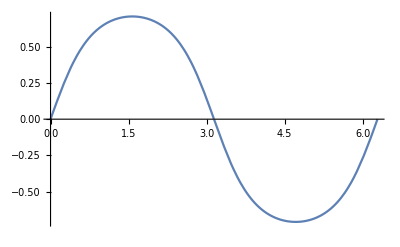

```mathematica
Plot[dθ[χ],{χ,0,2π}]
```

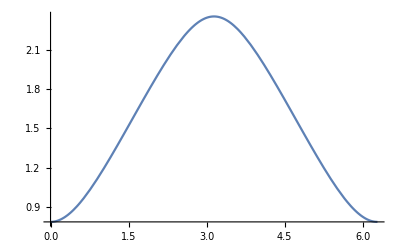

```mathematica
Plot[Θ[χ],{χ,0,2π}]
```

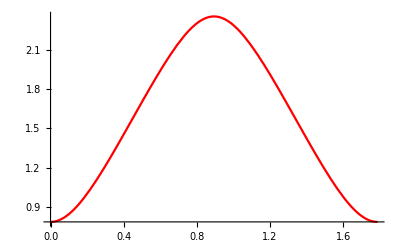

```mathematica
Plot[θt[t],{t,0,2 π/Freqs[[2]]},PlotStyle->{Red}]
```

```mathematica
((π/4)+.795)/(π/2) (*See origin of Subscript[θ, inc] https://arxiv.org/abs/gr-qc/0509101*)
```

1.00611

```mathematica
Tθ=tp[2π]
Δϕ=ϕp[2π]
```

212.027

6.63173

```mathematica
Ωθ=(2π)/Tθ
Freqs[[2]]
```

0.0296339

0.0296339

```mathematica
Ωϕ=Δϕ/Tθ
Freqs[[3]]
```

0.0312778

0.0312778

```mathematica
ω = m Ωϕ + k Ωθ
```

```mathematica
S[θ_]:=SpinWeightedSpheroidalHarmonicS[0,l,m,a ω,θ,0];
```

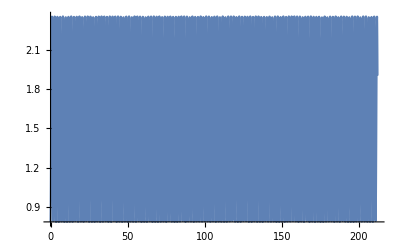

```mathematica
-(2 Ωθ)/r0 NIntegrate[S[θp[χ]]/ut[θp[χ]] Cos[ω tp[χ]-m ϕp[χ]]dt[χ],{χ,0,2π}]
```